# 医学生物学分野における高被引用論文の構造的特徴と長期的影響

## 要旨

本研究は、医学生物学分野における高被引用論文の長期的な引用ダイナミクスおよび構造的特徴を明らかにすることを目的とする。従来の計量書誌学では、3年・5年インパクトファクターのような短期的引用指標が主に用いられてきたが、論文の真の影響を把握するには長期的観察が不可欠である。本研究では、単なる被引用数ではなく、引用寿命、雑誌構造、研究テーマ構造といった多層的観点から分析を行った。
データにはPubMed annual baseline (2023) を用い、1946年から2020年までに出版された約3000万件の論文に記載されるレファレンス情報を対象とした。分析手法として、5年間ごとの「累積世代モデル」を構築し、被引用数上位1%の論文を「高被引用論文」と定義した。また、一般論文との比較のために4分位グループを設定した。
分析の結果、高被引用論文の中でも、最多被引用論文は数十年にわたり引用が持続し、オブソレッセンス（引用減衰）に至らない長寿命型の論文が存在することが確認された。一方、引用減衰が確認された高被引用論文も存在し、これらは出版から被引用ピークまで約4年、被引用ピークから減衰まで約7年という寿命構造が観察され、生物分野における既存モデルと整合的であった。しかし階層クラスタリングの結果、明確なタイプ分化は確認されなかった。
雑誌レベルでは、高被引用論文を多く掲載する雑誌が必ずしも高インパクトファクター誌であるとは限らないことが示された。ただし、Kullback–Leibler divergence による分析から、高被引用論文は他グループと比較して特定雑誌への集中傾向（嗜好）が強いことが明らかとなった。
研究テーマ構造の分析では、HeSHディスクリプターを使ったエントロピーの分析から、高被引用論文は他グループと比較して研究テーマが集中的であり、それを引用する論文の研究テーマもまた集中的であることが明らかになった。一方で研究テーマとそれを引用する論文のテーマの間には乖離が見られ、異なる分野から引用されやすい傾向にあることが明らかになった。

## 1. 背景と目的

計量書誌学においては3年インパクトファクターや5年インパクトファクターなど[Cla1]、特定の期間の引用をもとにした指標が多く用いられる。これは一面的には評価の公正性を考慮したものと考えられる。つまり、より古い論文ほど被引用数は多くなり、この「論文の年齢」による効果を差し引くためである。このような視点は雑誌の選定などにおいて重要なものである。一方で、長期に渡る引用の変化を把握することもまた重要である。第一に、前述の公正性における評価期間の設定の根拠となる。次に、短期的には捉えられない累積的な効果を捉えるには真に長期の観察が必要である。また、引用という現象をより深く捉えるためには、単に（被）引用数に着目するだけでなく、引用関係などのこれらの構造的な面へのアプローチが望まれる。本研究では以上のような視座にたち、長期的な引用のダイナミクスを明らかにすることを試みる。

## 2. 関連研究

高被引用論文や引用指標の研究は、近年も幅広い観点から進展している。Liら[Li1]は2300万論文を対象に長期にわたる引用の特徴を分析しグループ構造を明らかにした。また、Yuら[Yu1]は社会心理学分野のトップ被引用論文100本を対象とした構造解析により、主要な出版年・国際協力・ジャーナルの影響構造を明らかにし、被引用論文の研究ネットワーク構造に関する新しい知見を提供している。 雑誌レベルに注目したものとして、Leydesdorff[Le1-4]は雑誌間の関係マップを構築・調査した。天野ら[Am1-2]は医学生物学雑誌の大規模クラスタリングを行い、分野間の引用関係を明らかにした。こうした研究は、高被引用論文がどのような条件下で生まれ、どのような影響経路を持つかをマクロ的視点で捉える試みとして注目される。一方で、論文レベルの被引用性に寄与する構造的因子の体系化も進んでおり、共同研究形態・出版戦略・研究資源配分などの多要因が被引用性に影響する可能性が示唆されている。Hillら[Hil1]は、研究者の研究テーマの転換戦略はむしろその後の影響力を減少させる可能性を指摘した。Linら[Lin1]は、被引用論文の全文データを用いて、引用の位置・文脈・引用者との類似性が経時的に変化する現象を観察し、単なる引用数では捉えきれない引用役割の変容を指摘している。Koushaら[Ko1]は、情報科学分野の論文に対し、抄録の「読みやすさ」と論文の「質」が、被引用数にどのように影響するかを調査した。以上紹介した研究は主として被引用性にかかるさまざまな属性の特徴を明らかにするものであるが、高被引用論文に共通する長期的構造特性そのものを多層的に捉える研究は限定的である。本研究は、引用寿命・雑誌構造・テーマ構造（異分野引用）などの要素を統合的に分析することで既存研究とは異なる視点を提供する。

## 3. マテリアル

本研究では、長期的な引用ダイナミクスを把握するため、単年ごとの分析ではなく、引用の累積的効果を反映する「累積世代モデル」を構成する。またPubMedには各論文に統制語（MeSH）が付与されているため、高被引用論文に付与MeSHディスクリプターを計量的に分析することにより、研究テーマに関するマクロな構造を見出せると期待される。

### 3.1 データ

本研究ではFTP版のPubMed annual baseline (2023)（以降、PubMedとする）[PM1]を利用する。PubMedの論文登録数の推移を表1に示す。本研究の対象は、図1に示す1946年から2020年までに出版された論文約3000万件に記載されるレファレンス情報である。

表1

PubMedのレコード数

論文数 | 雑誌数 | 最初の論文出版年 | 最後の論文出版年
36,555,430 | 36,943 | 1781 | 2024

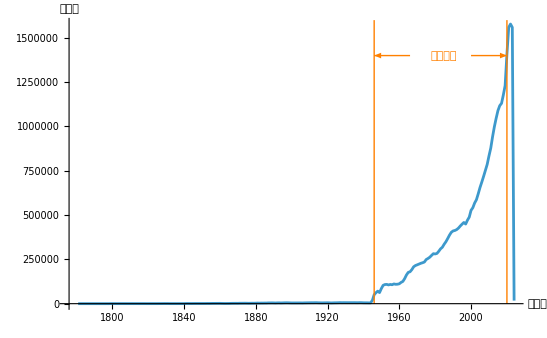

図1

PubMedの登録論文数の推移

### 3.2 累積世代モデルの構成

本研究では累積的な変化を捉えるために累積的な世代を構成する。まず、1946-2020の出版年をオーバーラップなしの5年ごとの区切りとし、15層を構成する。本研究ではこれらを累積的に用い、これを累積世代モデルと称する。構成前の各層の登録論文数、うち参考文献を持つ論文数、引用された論文数、引用数、雑誌数を図2に示す。雑誌数以外は指数関数的な増加を示している。

-Graphics-

図 2

5年ごとの登録論文数

### 3.3 高被引用論文・高被引用論文掲載誌・高被引用テーマ

本研究では、被引用数全体の1%を構成する被引用数上位の論文群を「高被引用論文」と定義する。これらを掲載した雑誌を「高被引用論文掲載誌」、高被引用論文に付与されるMeSHディスクリプターを「高被引用テーマ」と呼ぶ。さらに高被引用論文を引用する論文群を考え、これらの論文に付与されるMeSHディスクリプターを「高被引用論文引用テーマ」とする。また、論文に付与されるMeSHディスクリプター一般を「研究テーマ」、論文を引用する論文に付与されるMeSHディスクリプター一般を「引用テーマ」とする。以上の定義をまとめたものを表2に示す。本研究ではこれらを累積世代モデルに基づき集計する。

表2

本研究での用語定義

高被引用論文 | 被引用数全体の1%を構成する被引用数上位論文。
高被引用論文掲載誌 | 高被引用論文を出版した雑誌。
高被引用テーマ | 高被引用論文に付与されるMeSHディスクリプター。
高被引用論文引用テーマ | 高被引用論文を引用する論文に付与されるMeSHディスクリプター。
研究テーマ | 論文に付与されるMeSHディスクリプター。
引用テーマ | 論文を引用する論文に付与されるMeSHディスクリプター。

### 3.4 比較グループ

のちの章において高被引用論文とその他の論文とを比較するため、高被引用論文を含め全4グループを構成する。前述の高被引用論文をグループ1（G1）とし、同様に被引用数全体を100分した際の上位25-26分位区間にある論文群をG2、50-51分位区間にある論文群をG3、75-76分位区間にある論文群をG4とする。

## 4. 高被引用論文と経年的な引用の効果

### 4.1 高被引用論文の出現

高被引用論文の出現数を図3に示す。高被引用論文数および新規出現高被引用論文数は1946-2010年の累積世代以降に急増しているが、これは近年の収録論文数の急増を受けたものであると思われる。高被引用論文の影響性を確認するため、高被引用論文の全論文に占める割合を図4に示す。被引用数の1%を最大でも全体の0.0035%の論文が構成しており、集中度の高さが観察される。経時変化には一定の傾向はなく緩やかな変動がある。高被引用論文の入れ替わりを確認するため、新規高被引用論文の高被引用論文に占める割合を図5に示す。経時変化に一定の傾向はないが、10%から60%の間で順位の入れ替わりが観察される。

-Graphics-

図3

高被引用論文および新規出現高被引用論文の出現数

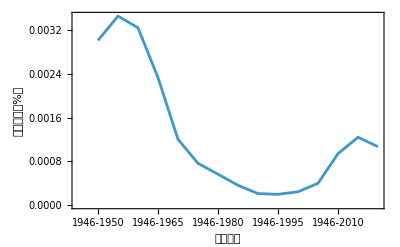

図4

高被引用論文の全論文に占める割合（%）

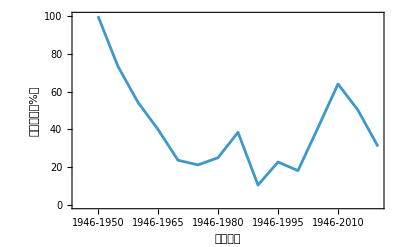

図5

新規出現高被引用論文の高被引用論文に占める割合（%）

### 4.2 最多被引用論文の変遷

各累積世代の最多被引用論文とその被引用数を表3に示す。最多被引用論文は累積世代が進んでも引き続き引用され続ける傾向があり、数十年をかけてインパクトを上昇させている。このため最多被引用論文の交代は少ない。論文タイトルおよび高被引用テーマを見る限りタンパク質に関するものであり、被引用が多い研究領域も論文と同様に累積世代が進んでも引き続き引用され続ける傾向があるのかもしれない。

表3

最多被引用論文タイトル

累積世代 | 高被引用論文タイトル | 高被引用論文掲載誌タイトル | 高被引用テーマ | 被引用数 | 当該累積世代の
高被引用論文数
1946-1950 | Qualitative analysis of proteins: a partition chromatographic method using paper. | The Biochemical journal | - | 74 | 10
1946-1955 | Same as above | Same as above | Same as above | 154 | 30
1946-1960 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | Molybdenum
Phenols
Plant Extracts
Proteins
Tungsten Compounds | 300 | 46
1946-1965 | Same as above | Same as above | Same as above | 1190 | 50
1946-1970 | Same as above | Same as above | Same as above | 3876 | 38
1946-1975 | Same as above | Same as above | Same as above | 9632 | 33
1946-1980 | Same as above | Same as above | Same as above | 17763 | 32
1946-1985 | Same as above | Same as above | Same as above | 25451 | 26
1946-1990 | Same as above | Same as above | Same as above | 32371 | 19
1946-1995 | Same as above | Same as above | Same as above | 37576 | 22
1946-2000 | Same as above | Same as above | Same as above | 40229 | 33
1946-2005 | Same as above | Same as above | Same as above | 42101 | 66
1946-2010 | Same as above | Same as above | Same as above | 44884 | 192
1946-2015 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4. | Nature | Autoradiography
Carbon Isotopes
Coliphages
Electrophoresis, Disc
Genes
Genetics, Microbial
Kinetics
Viral Proteins | 49961 | 315
1946-2020 | Same as above | Same as above | Same as above | 54249 | 336

### 4.3 高被引用論文への長期的な引用の効果

ここでは、個別の高被引用論文が長期的に影響を持つかどうかを検証するため、その寿命構造を分析する。まず、オブソレッセンス状態への到達を判定するために、P.D.B Paroloら[Par1]の長期被引用モデルおよびD. Wangら[Wan1]の被引用減衰モデルを前提とし、次の3つの条件を設定する： 1. 出版年から十分な期間がある、2. ピーク期が十分に過ぎ去っている、3. 被引用が十分に減衰している。これら3つの条件の具体的な設定値を図6に示す。この判定の結果、536論文中77論文がオブソレッセンス状態にあると判定された。オブソレッセンス状態にあると判定された高被引用論文および高被引用論文全体の、経過年にかかる指標値を図7に示す。オブソレッセンス状態にあると判定された論文では出版からピークまでの期間のモードは4年、ピークから被引用の十分な減衰までの期間のモードは7年、出版から被引用の十分な減衰までの期間のモードは12年であった。この結果は、P.D.B Paroloらの報告（生物分野では出版後5年以内にピークが訪れる）を支持している。一方、高被引用論文全体では出版からピークまでの期間は10年付近であり異なる様相を示している。オブソレッセンス状態にあると判定された高被引用論文における被引用数のプロットを図8に示す。出版から被引用が十分に減衰するまでの期間は最小で10年、最大で84年であった。同図からは近年の論文ほど出版直後に高い被引用を受ける傾向があると推測される。
次に、オブソレッセンス状態にあると判定された高被引用論文について、その群内で特徴差があるのかを確認するため、階層クラスタリングを行った。クラスタリングに用いた特徴量は、a. 経過年に関する指標としてa-1:出版からピークまでの期間（Peak period）、a-2:ピークから被引用の十分な減衰が見られるまでの期間（Decay period）、b.被引用の寄与に関する指標としてb-1:ピーク年の被引用数（Peak count）、b-2:減衰年までの被引用数合計（Decay cited: A+B）、c.被引用の安定性に関する指標としてc-1:毎年の被引用数の分散（Variance:cited）、c-2:毎年の被引用速度の分散（Variance:diff）、c-3:毎年の引用加速度の分散（Variance:diff-accel）（以上、7指標）である。距離にはユークリッド距離を用い、各指標値にはノーマライズを行った。分散の計算においては先頭に0-パディングを行った5年平均を用いた。この結果を図9に示す。クラスタリングではノードが集中的に存在する領域といくつかのノードがまばらに見られる周辺領域が観察されるが、明確な分割構造は確認できなかった。
また、表3に示される最多被引用論文はいずれもオブソレッセンス状態にあると判定されなかった。これら3件の論文における、各指標値を表4に、被引用数の経年プロットを図10に示す。いずれの論文も出版からピークまでの期間が非常に長く、かつ、いまだに毎年十分な数の被引用がある。うち2件の論文（Protein measurement with ... と Cleavage of structural proteins ...）については多峰性が見られ、被引用の傾向も似通っている。

表4

最多高被引用論文におけるオブソレッセンスにかかる指標

論文タイトル | 最大被引用を得るまでの期間 | 減衰期間 | 最大被引用数（年間） | 減衰年の被引用数 | 被引用数分散 | 被引用速度の分散 | 被引用か速度の分散
Qualitative analysis of ... | 9 | 5 | 23 | 177 | 28.4 | 1.2 | 0.6
Protein measurement with ... | 28 | 10 | 1740 | 29743 | 256971. | 5510.1 | 605.6
Cleavage of structural proteins ... | 23 | 5 | 2261 | 32245 | 380198. | 12712.1 | 1212.2

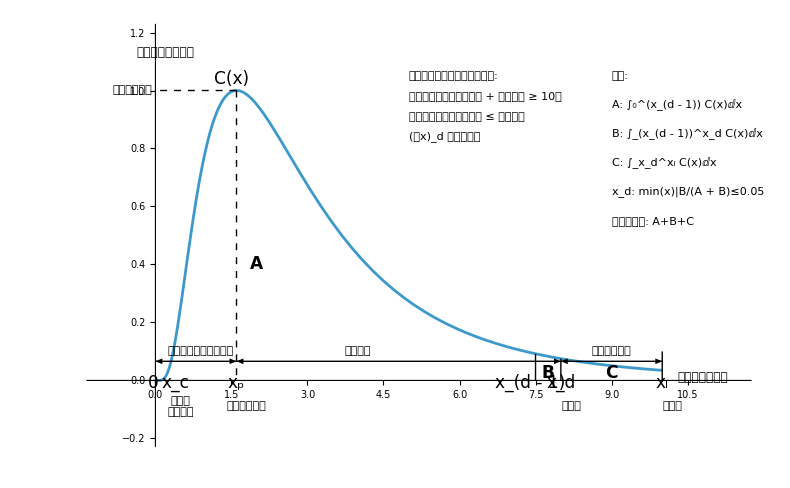

図6

オブソレッセンスモデル、指標値および選択条件

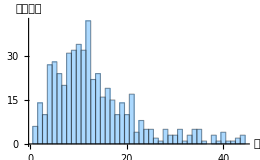
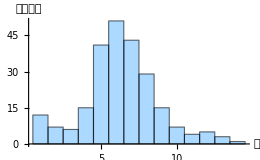
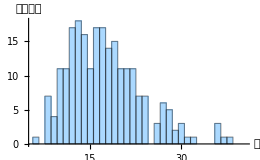
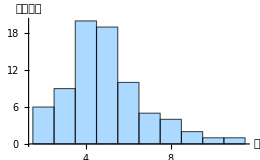
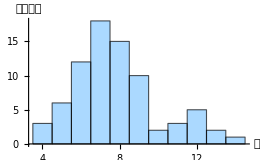
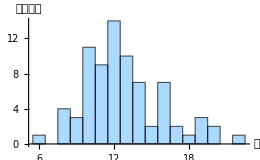
高被引用論文全体 | -Graphics- | -Graphics- | -Graphics-
オブソレッセンス状態
にある論文のみ | -Graphics- | -Graphics- | -Graphics-

図7

高被引用論文のオブソレッセンスにかかる指標値

「ピークから減衰までの年」および「出版から減衰までの年」については、減衰が観測された論文のみで集計した。

-Graphics3D-

図8

オブソレッセンス状態にある高被引用論文の被引用数

出版された年を0として1年ごとの被引用数をプロットした。

-Graphics-

図9

十分な引用減衰が確認された高被引用論文の階層クラスタリングとPCAプロット

標準化した7指標（前述）のユークリッド距離による階層クラスタリングを構成し、別途PCA（PC1-PC3）プロットによる分布を確認した。メンバーのマジョリティを緑のドットで、周辺のメンバーを赤のドットで表す。周辺のメンバーはクラスタリング木の右端のメンバー（ID:46,49,38,51,43）に対応する。明確なクラスターは見出せない。

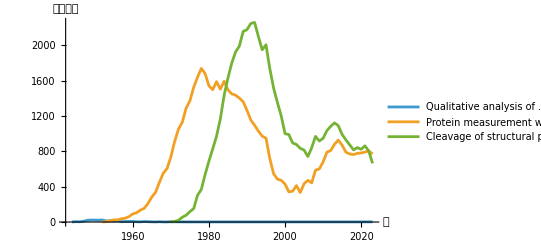

図10

最多被引用論文タイトルの被引用数の推移

括弧内の数字は出版年を示す。3タイトルはいずれも被引用の十分な減衰が確認されなかった。また、うち2タイトルについては多峰性が見て取れる。

## 5. 高被引用論文掲載誌

これまで論文単位で観察してきたが、引用の構造は出版媒体（雑誌）という制度的単位とも深く関係している。そこで次に、論文レベルの現象が雑誌レベルでどのように現れるかを検討する。

### 5.1 高被引用論文掲載誌の出現

高被引用論文掲載誌の出現数を図11に示す。高被引用論文掲載誌数および新規出現高被引用論文掲載誌は1946-2010年の累積世代以降に急増しており、前述した高被引用論文数の急増のタイミングと一致する。高被引用論文の掲載誌の影響を確認するため、高被引用論文掲載誌の全雑誌に占める割合を図12に示す。経時変化に一定の傾向はなく緩やかな変動が観察される。高被引用論文掲載誌の入れ替わりを確認するため、新規出現高被引用論文掲載誌の高被引用論文掲載誌に占める割合を図13に示す。経時変化に一定の傾向は観察されず、かつ、激しい変動が観察される。

-Graphics-

図11

高被引用論文掲載誌および新規出現高被引用論文掲載誌の出現数

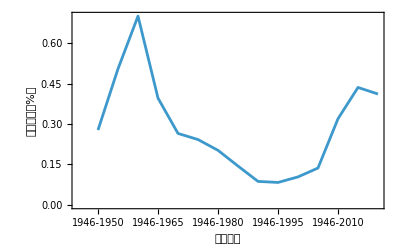

図12

高被引用論文掲載誌の全雑誌に占める割合（%）

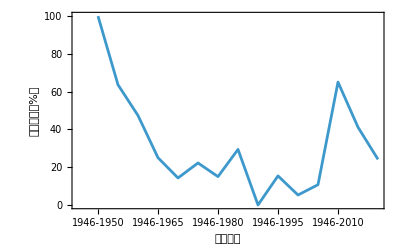

図13

新規出現高被引用論文掲載誌の高被引用論文掲載誌に占める割合（%）

### 5.2 高被引用論文掲載誌の変遷

ここでは高被引用論文掲載誌の変化を高被引用でないグループのそれと比較する。G1-G4の当該論文の掲載数上位の雑誌一覧を表5に示す。各誌のインパクトファクターとその発表年についてはJournal Citation Reports  (JCR）[JCR1]から求めた。JCRではインパクトファクターの公開が1997からであるため、1946-2000年の累積世代以降についてのみ、累積世代の最終年のインパクトファクターを求めた。ここから、高被引用論文を持つ雑誌は必ずしもインパクトファクターが高い雑誌ではないことがわかる。一方、グループ間での雑誌の構成においては明確な差異は認めらない。そこで、各グループでどの程度の雑誌の嗜好があるかを確認するため、全てのグループを合成した集団と各グループとの間でのKullback–Leibler divergence（KLD）をを図14に示す。図14からは、高被引用論文は他のグループに比べ雑誌の嗜好が強いことがわかる。

表5-1

高被引用論文掲載誌のうち最大の論文数を持つもの

累積世代 | 雑誌タイトル | 当該誌の
高被引用論文数 | 当該誌の高被引用論文が
当該累積世代の高被引用論文
全体に占める割合(%) | IF | /IF発表年
1946-1950 | The Journal of clinical investigation
The Biochemical journal | 3
3 | 30 | 12.015/2000 | 15.053/2005 | 14.152/2010 | 12.575/2015 | 14.808/2020
4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1955 | The Biochemical journal | 13 | 43 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1960 | The Biochemical journal | 11 | 24 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1965 | The Biochemical journal | 13 | 26 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1970 | The Biochemical journal | 9 | 24 | 4.28/2000 | 4.224/2005 | 5.016/2010 | 3.562/2015 | 3.857/2020
1946-1975 | The Journal of biological chemistry | 7 | 21 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1980 | The Journal of biological chemistry | 7 | 22 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1985 | The Journal of biological chemistry | 5 | 19 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1990 | The Journal of biological chemistry | 4 | 21 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-1995 | The Journal of biological chemistry | 4 | 18 | 7.368/2000 | 5.854/2005 | 5.328/2010 | 4.258/2015 | 5.157/2020
1946-2000 | Journal of molecular biology
Proceedings of the National Academy of Sciences of the United States of America | 4
4 | 12 | 5.388/2000 | 5.229/2005 | 4.008/2010 | 4.517/2015 | 5.469/2020
10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
1946-2005 | Proceedings of the National Academy of Sciences of the United States of America | 8 | 12 | 10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
1946-2010 | Proceedings of the National Academy of Sciences of the United States of America
Nature | 14
14 | 7 | 10.789/2000 | 10.231/2005 | 9.771/2010 | 9.423/2015 | 11.205/2020
25.814/2000 | 29.273/2005 | 36.104/2010 | 38.138/2015 | 49.962/2020
1946-2015 | Nature | 20 | 6 | 25.814/2000 | 29.273/2005 | 36.104/2010 | 38.138/2015 | 49.962/2020
1946-2020 | Bioinformatics (Oxford, England) | 17 | 5 | 3.409/2000 | 6.019/2005 | 4.877/2010 | 5.766/2015 | 6.937/2020

表5-2

G2雑誌のうち最大の論文数を持つもの

累積世代 | 雑誌タイトル | 当該誌の
G2論文数 | 当該誌のG2論文が
当該累積世代のG2論文
全体に占める割合(%) | IF / 発表年
1946-1950 | Journal of bacteriology | 34 | 45 | 3.506/2000 4.167/2005 3.726/2010 3.198/2015 3.49/2020
1946-1955 | The Biochemical journal | 20 | 7 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1960 | The Biochemical journal | 64 | 10 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1965 | The Biochemical journal | 62 | 7 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1970 | The Journal of biological chemistry | 90 | 6 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1975 | The Journal of physiology | 98 | 5 | 4.455/2000 4.272/2005 5.139/2010 4.731/2015 5.182/2020
1946-1980 | The Journal of biological chemistry | 150 | 5 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1985 | Proceedings of the National Academy of Sciences of the United States of America | 214 | 6 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-1990 | Proceedings of the National Academy of Sciences of the United States of America | 316 | 7 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-1995 | Proceedings of the National Academy of Sciences of the United States of America | 410 | 7 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2000 | Proceedings of the National Academy of Sciences of the United States of America | 490 | 7 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2005 | Proceedings of the National Academy of Sciences of the United States of America | 715 | 7 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2010 | Proceedings of the National Academy of Sciences of the United States of America | 947 | 6 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2015 | Proceedings of the National Academy of Sciences of the United States of America | 882 | 5 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-2020 | Proceedings of the National Academy of Sciences of the United States of America | 810 | 3 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020

表5-3

G3雑誌のうち最大の論文数を持つもの

累積世代 | 雑誌タイトル | 当該誌の
G3論文数 | 当該誌のG3論文が
当該累積世代のG3論文
全体に占める割合(%) | IF / 発表年
1946-1950 | The Biochemical journal | 41 | 24 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1955 | The Journal of biological chemistry | 21 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1960 | Proceedings of the Society for Experimental Biology and Medicine. 
Society for Experimental Biology and Medicine (New York, N.Y.) | 71 | 5 | 3.415/2000 -/2005 -/2010 -/2015 -/2020
1946-1965 | The Journal of biological chemistry | 72 | 3 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1970 | The Journal of biological chemistry | 116 | 3 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1975 | The Journal of biological chemistry | 205 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1980 | The Biochemical journal | 267 | 4 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1985 | Proceedings of the National Academy of Sciences of the United States of America | 388 | 4 | 10.789/2000 10.231/2005 9.771/2010 9.423/2015 11.205/2020
1946-1990 | The Journal of biological chemistry | 440 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1995 | The Journal of biological chemistry | 782 | 5 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2000 | The Journal of biological chemistry | 897 | 5 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2005 | The Journal of biological chemistry | 1419 | 5 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2010 | The Journal of biological chemistry | 1681 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2015 | The Journal of biological chemistry | 1976 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2020 | The Journal of biological chemistry | 1678 | 2 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020

表5-4

G4雑誌のうち最大の論文数を持つもの

累積世代 | 雑誌タイトル | 当該誌の
G4論文数 | 当該誌のG4論文が
当該累積世代のG4論文
全体に占める割合(%) | IF / 発表年
1946-1950 | Annals of surgery | 34 | 10 | 5.987/2000 6.328/2005 7.474/2010 8.569/2015 12.969/2020
1946-1955 | Annals of surgery | 105 | 6 | 5.987/2000 6.328/2005 7.474/2010 8.569/2015 12.969/2020
1946-1960 | The Biochemical journal | 240 | 10 | 4.28/2000 4.224/2005 5.016/2010 3.562/2015 3.857/2020
1946-1965 | Nature | 121 | 3 | 25.814/2000 29.273/2005 36.104/2010 38.138/2015 49.962/2020
1946-1970 | British medical journal | 185 | 2 | 5.331/2000 9.052/2005 13.471/2010 -/2015 -/2020
1946-1975 | Biochimica et biophysica acta | 290 | 3 | -/2000 -/2005 -/2010 -/2015 -/2020
1946-1980 | Biochimica et biophysica acta | 489 | 3 | -/2000 -/2005 -/2010 -/2015 -/2020
1946-1985 | The Journal of biological chemistry | 627 | 3 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-1990 | Biochimica et biophysica acta | 842 | 3 | -/2000 -/2005 -/2010 -/2015 -/2020
1946-1995 | The Journal of biological chemistry | 1142 | 3 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2000 | The Journal of biological chemistry | 1770 | 4 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2005 | The Journal of biological chemistry | 1375 | 2 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2010 | The Journal of biological chemistry | 2093 | 2 | 7.368/2000 5.854/2005 5.328/2010 4.258/2015 5.157/2020
1946-2015 | PloS one | 3117 | 2 | -/2000 -/2005 4.411/2010 3.057/2015 3.24/2020
1946-2020 | PloS one | 3560 | 2 | -/2000 -/2005 4.411/2010 3.057/2015 3.24/2020

-Graphics-

図14

各グループの雑誌の構成に関するKLD

## 6. 高被引用テーマ

以上のように、出版誌という観点からは、高被引用論文は高被引用でない論文に比べ雑誌の嗜好が強いことがわかった。ここでは、視点を変え、研究内容に関する構造的な差を明らかにするため、論文のテーマに着目する。

### 6.1 高被引用テーマの出現

高被引用テーマのユニーク出現数を図15に示す。2023年MeSHディスクリプターの総数はおよそ30000であるが、各累積世代における高被引用テーマの出現数は最大でも3000を超える程度であり高被引用テーマには集中が見られる。高被引用テーマの入れ替わりを確認するため、新規出現高被引用テーマの高被引用テーマ全体に占める割合を図16に示す。経時的に一定の傾向は観察されず、数%から十数%の範囲での入れ替わりが観察される。なお、1946-1955年の累積世代に高い値が見られる理由は、前累積世代ではMeSHディスクリプターの付与がほとんどなかったためである。

-Graphics-

図15

高被引用論文に付与された高被引用テーマの種数

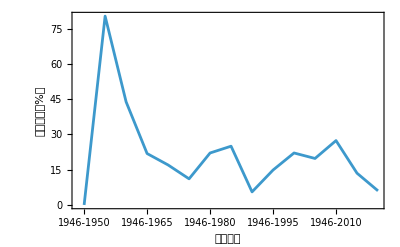

図16

新規出現高被引用テーマの高被引用テーマ全体に占める割合（%）

### 6.2 高被引用テーマの変遷

ここでは高被引用テーマの変化を、高被引用でない論文の研究テーマ（または引用テーマ）と比較する。
各累積世代、各グループごとの最頻出研究テーマと引用テーマを表6に示す。これらのうちG1の研究テーマ（高被引用テーマ）にのみにバラエティが確認される。
次に、各累積世代の研究テーマと引用テーマの多様性を見るために各グループのエントロピーの変化を観察した。研究テーマ、引用テーマ、研究テーマと引用テーマ対の出現数のエントロピーを、それぞれ図17に示す。計数の方法は研究テーマと引用テーマはそれぞれ論文ごとの分数カウントを採用した。研究テーマ対引用テーマのペアについては、ひとつの参照ごとに研究テーマと引用テーマの2部グラフを構成し、エッジの重みの合計が1となる分数カウントを採用した。図18からは高被引用論文のみがエントロピーが低く、その他のグループ間ではそれほど差がないことがわかる。なお、1946-1950年の累積世代に関してはMeSHディスクリプターの付与数が十分でなかったため除外している。
また、研究者の引用行動は必ずしも当該論文と同じテーマを引用するものではない。この転換の程度を見るために、グループごとに研究テーマと引用テーマのコサイン距離を観察した。この結果を図18に示す。こちらも高被引用論文のみが他とは異なる様相を示した。また、高被引用論文は1946-2010年の累積世代以降、転換の程度は減少傾向にあり、他のグループとの差はなくなりつつあるように推察される。さらに、各累積世代間に対しても研究テーマの転換の程度を確認するために、各グループの累積世代間の研究テーマのコサイン距離を観察した。累積世代間では論文集合のメンバーが異なるので論文集合全体のテーマの重み付カウントを用いた。この結果を図19に示す。これによれば累積世代間のテーマの転換の程度は一定の傾向を示さなかったが、グループ2のみが常に低い転換の程度を保っている。
以上より、高被引用テーマには次の特徴があると考えられる：(1)高被引用論文は異なるテーマから引用されやすい。このことは表6の最頻出テーマから予想され、図19に示す転換の程度もこれを裏付けている。(2)高被引用論文は研究テーマが集中的であり、それを引用する論文の研究テーマもまた集中的である。このことは図18から示唆される。(3)高被引用論文の累積世代間の研究テーマの転換度は他のグループに比べやや高いと考えられる。このことは表6では高被引用テーマのみにバラエティが観察され、図19においてもやや高い数値が観察されることによる。

表6

累積世代ごと論文グループごとの最頻出テーマ

1946-1955
1946-1960
1946-1965
1946-1970
1946-1975
1946-1980
1946-1985
1946-1990
1946-1995
1946-2000
1946-2005
1946-2010
1946-2015
1946-2020 | G1
引用テーマ | 
研究テーマ
Humans | Insulin
Humans | Blood Proteins
Animals | Microscopy, Electron
Animals | Microscopy, Electron
Animals | Microscopy, Electron
Animals | Proteins
Animals | Proteins
Animals | Proteins
Animals | Base Sequence
Animals | Base Sequence
Animals | Base Sequence
Animals | Humans
Humans | Humans
Humans | Humans | G2
引用テーマ | 
研究テーマ
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Animals | Humans
Animals | Animals
Animals | Humans
Animals | Animals
Humans | Animals
Humans | Humans
Humans | Humans
Humans | Humans | G3
引用テーマ | 
研究テーマ
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Animals
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans | G4
引用テーマ | 
研究テーマ
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Animals
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans

-Graphics--Graphics--Graphics-

図17

累積世代、論文グループごとの研究テーマの出現に関するエントロピー

1946-1950年の累積世代では十分なMeSHディスクリプターの付与がなかったため対象外とした。

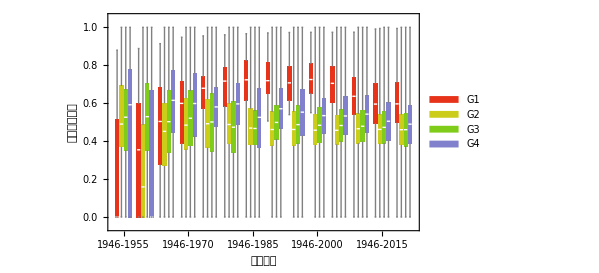

図18

累積世代、論文グループごとの研究テーマに対する引用テーマの転換の程度

箱ひげ図の区間は、下から最小値、25%分位点、中央値、75%分位点、最大値となる。1946-1950年の累積世代では十分なMeSHディスクリプターの付与がなかったため対象外とした。

-Graphics-

図19

論文グループごとの累積世代間の研究テーマの転換の程度

1946-1950年の累積世代では十分なMeSHディスクリプターの付与がなかったため対象外とした。

## 7. まとめ

高被引用論文の順位変化とオブソレッセンス

高被引用論文はその被引用の累積的な効果により長期にわたり上位の順位を維持するものの、やがては新しい累積世代の論文にその座を明け渡す現象を確認できた。この交代までの被引用の累積的な効果には非常に長いものが多く最長で50年以上であった。また、これらのうちの多くの論文は順位を落としつつも引き続き引用を受けていた。一方、高被引用論文のうちでも被引用の十分な減衰が観察されたものがあり、これらの被引用の傾向（出版から被引用のピークまでのモードや被引用の長期変化の形状）は過去の報告を裏付けるものであった。

高被引用論文掲載誌の特徴

長期にわたる引用を考慮した、本研究の定義による高被引用論文は、必ずしも高いインパクトファクターの雑誌に掲載されるわけではないことが明らかになった。高被引用論文掲載誌はインパクトファクターを見れば3-50と幅広いが、G2-G4の雑誌群では3-10程度である。一方で掲載誌への嗜好は他のグループに比べて強い。また、実際にはよりインパクトファクターが高い雑誌が存在するにもかかわらず、本研究では高被引用論文掲載誌の中にはそのような雑誌の出現を確認できなかった。

高被引用テーマと高被引用論文引用テーマ

高被引用論文は、研究テーマが集中的であり、異なるテーマの論文から引用されやすいことがわかった。高被引用論文は、研究テーマおよび引用テーマそれぞれを個別に見た場合の多様性は低いが、研究テーマ対引用テーマの転換という観点では乖離が見られた。もしこれがオブソレッセンスに影響しているのだとすれば、様々な研究領域から興味を持たれるようなテーマの論文は”長生き”するのかもしれない。

長期的な傾向

高被引用論文/高被引用論文掲載誌/高被引用テーマの増加や構成については特段の傾向は見られなかった。最頻出テーマの傾向としては、高被引用テーマ（G1の研究テーマ）にのみ入れ替わりがみられその他は安定して一つから二つのテーマが見られる。研究テーマ/引用テーマの多様性（エントロピー）はすべてのグループで経時的に上昇傾向にあり、G1のみが他と比べて低い。研究テーマ対引用テーマの転換の程度はいずれのグループでも経時的に安定しているが、G1のみにやや異なる挙動が見られる。累積世代間の研究テーマの転換の程度は安定しておらず、特段の傾向は見られない。

## 参考

[Am1] 天野晃;児玉閲;柴田大輔;小野寺夏生. 引用データに基づく自然科学領域における学術研究分野間の関係. 情報メディア研究. 2013, Vol 12, No. 1, p. 28-41.

[Am2] 天野晃;児玉閲. 引用にもとづく雑誌クラスタリング法の開発. 情報メディア研究. 2008, Vol 7, No. 1, p. 63-73.

[Cla1] The Clarivate Impact Factor. https://clarivate.com/academia-government/essays/impact-factor . (accessed 2025.07.01)

[Hil1] Ryan Hill, Yian Yin, Carolyn Stein, Xizhao Wang, Dashun Wang, Benjamin F. Jones. The pivot penalty in research. Narure. 2025, Vol. 642, p. 999-1006.

[JCR1] Journal Citation Reports. https://jcr.clarivate.com/jcr/home . (accessed 2024.07.01)

[Ko1] Kayvan Kousha, Mike Thelwall. Factors associating with or predicting more cited or higher quality journal articles: An Annual Review of Information Science and Technology (ARIST) paper. Journal of Association for Information Science and Technology. 2024. Vol. 75 No. 3, p. 215-244.

[Le1] Leydesdorf, L. Various methods for the mapping of science. Scientometrics. 1987, Vol. 11, Nos 5-6, p. 295-324.

[Le2] Leydesdorf, L. Clusters and maps of science journals based on bi-connected graphs in Journal Citation Reports. Journal of Documentation. 2004, Vol. 60, No. 4, p. 371-427.

[Le3] Leydesdorf, L. Indicators of structual change in the dynamics of science: Entropy statisitics of the SCI Journal Citation Re- ports. Scientometrics. 2002, Vol. 53, No. 1, p. 131-159.

[Le4] Leydesdorf L. Can scientific journals be classified in terms of aggregated journal- journal citation relations using the Journal Citation Reports? Journal of the American Society for Information Science and Tech- nology. 2006, Vol. 57, No. 5, p. 601-613.

[Li1] Xin Li, Xuli Tang. How biomedical papers accumulated their clinical citations: a large-scale retrospective analysis based on PubMed. 2024. Vol 129, p. 3315–3339.

[Lin1] Gege Lin, Nees Jan van Eck, Haiyan Hou, Zhigang Hu. The changing role of cited papers over time: An analysis of highly cited papers based on a large full-text dataset. ArXiv. 2025, https://doi.org/10.48550/arXiv.2509.04190

[Par1] P.D.B. Parolo, et.al. Attention decay in science. Journal of Informatics. 2015. Vol.9, p.734-745.

[PM1] PubMed https://pubmed.ncbi.nlm.nih.gov/ . (accessed 2025.07.01)

[Yu1] Shu Yu, Ke Chen. A bibliometric and altmetric analysis of the top 100 most cited articles in social psychology (2000–2024).  Discover Psychology. 2006, Vol. 6 No. 28. https://doi.org/10.1007/s44202-025-00557-8

[Wan1] Dashun Wang, Chaoming Song, Albert-László Barabási. Quantifying Long-Term Scientific Impact. Science. 2013. Vol. 342, No. 127. DOI: 10.1126/science.1237825